```mathematica
(*Taylor - aproskimacija*)
```

```mathematica
Clear[f,n]
```

```mathematica
f[t_]:=Sin[t]*t^2*E^-t
```

```mathematica
Manipulate[Show[
Plot[f[t],{t,0,4},PlotStyle->Red,AxesLabel->{"x","y"},PlotLegends->{"f(t)"}],
Plot[Evaluate[Normal[Series[f[t],{t,2,n}]]],{t,0,4},PlotStyle->Blue, AxesLabel->{"x","y"},PlotLegends->{"Taylor n=" <>ToString[n]}],PlotRange->All],
{n,1,10,1}]
```

```mathematica
(*Izračunan približek π*)
```

```mathematica
Get[NotebookDirectory[]<>"Datotečna_funkcija.m"];
dat=Datoteka[10000];
{vKrogu,izvenKroga}=dat;
{piAproks,napaka}=areaPi[vKrogu,10000];
```

```mathematica
(*Izpis aproksimacije in napake*)
```

{3.1524 = aproksimiran π,0.0108073 = napaka}

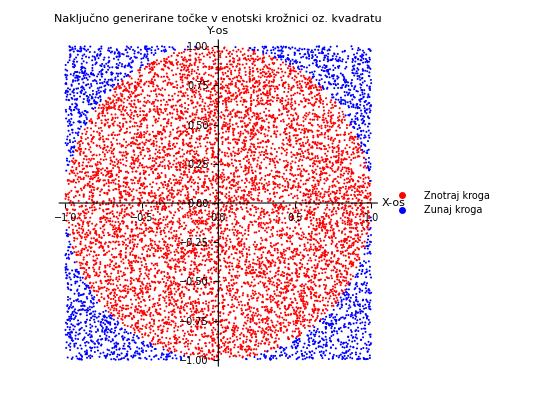

```mathematica
Print[{"= aproksimiran π" N[piAproks],"= napaka" N[napaka]}];

(*Prikaz grafa*)
Show[ListPlot[{vKrogu,izvenKroga},PlotStyle->{Red,Blue},PlotLegends->{"Znotraj kroga","Zunaj kroga"},AxesLabel->{"X-os","Y-os"},PlotLabel->"Naključno generirane točke v enotski krožnici oz. kvadratu",AspectRatio->Automatic]]
```